## Empowering Research with Large Language Models: A Practical Guide for PhD Students Across Disciplines

Large Language Models (LLMs) are transforming the research landscape by offering a new set of tools that streamline common tasks, enabling PhD students to work smarter and faster. This talk explores how researchers in diverse fields can leverage LLMs like OpenAI’s GPT, Anthropic’s Claude, X.ai’s Grok, and Gemini to enhance their work. We will cover practical applications for PhD students, such as literature review, brainstorming ideas, generating visuals, and data analysis, showcasing not only the major LLM providers but also powerful free and local options like those accessible via Ollama and NotebookLM.

You’ll learn about both API-driven and local deployments, enabling adaptable and affordable/free solutions regardless of your research environment. From automating tedious tasks to accelerating programming and complex modeling, we will explore a toolkit that every researcher can harness to maximize efficiency and creativity. By the end of this session, attendees will be equipped with insights and hands-on knowledge on how to integrate these models into their research workflows, making the journey from idea to publication smoother, more innovative, and more collaborative.

# Marco Thiel office: Meston Building 332 Email: m.thiel@abdn.ac.uk Tel: 01224 27 3160 (defunct) Office hours: Wednesday 1pm-2:00pm on Zoom Feedback link: https://wolfr.am/1qErIIeub 5 November, 2024

## The rise of AI/LLMs

```mathematica
ImageCollage[ConformImages[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}],Background->None]
```

-Graphics-

## They are coming for your jobs...

```mathematica
ImageCollage[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Background->None]
```

-Graphics-

## Humans can do...

```mathematica
Video[Import[NotebookDirectory[]<>"I robot clip Can you.mp4"]]
```

## Level 0 : Basic Tools

## Level 0 tools and how to use them: ChatGPT, Claude, Perplexity, OpenRouter

-Graphics-

#### ChatGPT

ChatGPT, developed by OpenAI, stands out as a versatile conversational tool with advanced capabilities for diverse applications. It includes specialized features such as Data Science capabilities, custom GPTs, and a visual tool, Canvas, to enhance productivity and creativity in research and data analysis.

use case 1: Good prompting

prompt: “I am a researcher trying to optimise the flow of patients through the hospital system. Hospitals are often understaffed, under-financed and overwhelmed by incoming patients. You are a senior administrator who as worked as consultant in an NHS hospital in Aberdeen (Scotland) for 20 years. You know the issues arising. I want you do come up with a project to study how to optimise the patient flow through the hospital. This might involve predicting the time a patient will spend within the system based on the initial diagnosis. I want you to describe the system as a “flow” of patients through various parts of the hospital and write a simple  piece of code in the Mathematica/Wolfram Language to simulate the flow. Answer in a professional tone, suitable for use in an application for funding.”

link:  https://chatgpt.com

outcome: https://chatgpt.com/share/e/6728f022-7230-8011-9627-d70776f8d69b

Average time per stage:

Average total time per patient: {101/2,168.711}

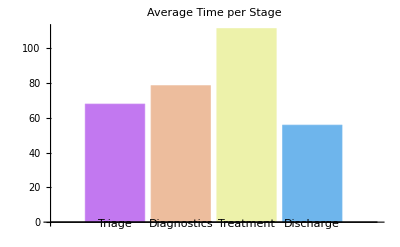

```mathematica
(*Parameters*)numPatients=100; 
(*Total number of patients*) hospitalStages={"Triage","Diagnostics","Treatment","Discharge"};

(*Average time spent at each stage (in minutes)*)
stageTimes=<|"Triage"->20,"Diagnostics"->45,"Treatment"->90,"Discharge"->15|>;

(*Random time variation at each stage*)
timeVariation=<|"Triage"->10,"Diagnostics"->15,"Treatment"->30,"Discharge"->5|>;

(*Initialize patient flow times*)
patientFlowTimes=Table[<|"PatientID"->i,"StageTimes"->{}|>,{i,1,numPatients}];

(*Simulate each patient's journey through hospital stages*)
patientFlowTimes=patientFlowTimes/. p:<|"PatientID"->i_,"StageTimes"->{}|>:>(<|"PatientID"->i,"StageTimes"->AssociationMap[(*Total time is the mean time for stage plus a random variation*)stage↦RandomVariate[NormalDistribution[stageTimes[stage],timeVariation[stage]]],hospitalStages]|>);

(*Aggregate total time per patient and per stage*)
totalTimes=Table[<|"PatientID"->p["PatientID"],"TotalTime"->Total[Values[p["StageTimes"]]]|>,{p,patientFlowTimes}];

(*Results summary*)
Print["Average time per stage:"];
averageTimes=AssociationMap[Mean[Values[#]]&,GroupBy[patientFlowTimes,#["StageTimes"]&,Mean]];

Print["Average total time per patient: ",Mean[Values[totalTimes]]];

(*Visualization of patient flow times*)
BarChart[Values[averageTimes],ChartLabels->Keys[averageTimes],ChartStyle->"Pastel",PlotLabel->"Average Time per Stage"]
```

use case 2: Prompt using Consensus

prompt: “Conduct a literature research about the cell cycle of S. cerevisiae.”

link: https://chatgpt.com

outcome: https://chatgpt.com/share/e/6728ec4d-4d50-8011-bf27-048c3cf58aa5

use case 3: Prompt using Whimsical Diagrams

prompt: “Find out what the phases of the cell cycle in S. cerevisiae are. Then draw a simple diagram of it.”; “Can you make this into a circular structure?”

link: https://chatgpt.com

outcome: https://chatgpt.com/share/e/6728ed31-b678-8011-98f2-b4684831685f

use case 4: Solving physics problems

prompt: -Graphics-

link: https://chatgpt.com

outcome: https://chatgpt.com/c/6728fc28-3830-8011-9b71-0643a6130678

expected outcome: -Graphics- and -Graphics-

use case 5: Data Analysis

prompt: Data Analyst. Uses lex.csv file. “Look at the data and summarise what they describe. Clean the data.”, “Use the PlotLy to make an interactive visualization of the data for download. ”, “There is a massive decrease in life expectancy in one of the countries in 1994. What is the country and speculate on why the life expectancy decreased that much!”

link:https://chatgpt.com

outcome: https://chatgpt.com/share/e/67290296-17a0-8011-a637-a54003e89dbb  and

```mathematica
SystemOpen[NotebookDirectory[]<>"Presentation LLMs for research/life_expectancy_interactive_plot.html"]
```

use case 6: Data Analysis 2

prompt: “Make a list of the first 40 Fibonacci numbers. Then fit a polynomial of 4th order. Plot the fit (in blue) and the data points (in red) into one diagram.” “What are the parameters of the fitted curve? Show an ANOVA table.”

link: https://chatgpt.com

outcome: https://chatgpt.com/share/e/67290518-7af4-8011-841c-907ae8fe3a22

#### Claude.ai

Anthropic’s Claude.ai is a high-level AI assistant designed for complex problem-solving and analysis. Its unique interface supports in-line code execution, allowing users to write and test code directly within conversations, which is particularly useful for research applications.

use case 1: Program the game Space Invaders

prompt: “Program the game space invaders in React. Make the game playable using the arrow keys. Make sure that it is not too fast or too slow. Make the invaders look like little monsters in red and the space ship like a little triangle in green. Make sure that each shot kills one invader, but not the entire column.”; “That is not bad, but the space ship is invisible, probably black. Make it green. Also the space ship moves too slowly.”

link: https://claude.ai/

outcome: https://claude.site/artifacts/24445f0f-aa3f-4f22-b1fb-395008d730bb

use case 2: Simulating the solar system

prompt: “Make a simulation of the solar system with the sun and all planets. Make the planet orbit times and the distances to scale. Make sure that the simulation is fast enough that I can comfortably see the outer planets move. Try to make the video appealing and useful.”; “The planets are too close together can you use more of the screen for the simulation?”, “The planets do not move along the orbit lines. The are still too close to the sun.The orbits do not same circular but flattened.”

link: https://claude.ai/

outcome: https://claude.site/artifacts/5758ae8d-9927-482a-a7e3-b3a1dd2dfb60

#### Perplexity.ai

Perplexity.ai is known for its powerful research-oriented interface, providing clear, cited answers to complex queries. It leverages web search and citation tools to offer reliable and well-sourced responses, making it ideal for academic and research settings.

use case 1: Literature on cell cycle

prompt: “I am doing research for a project modelling the cell cycle of S cerevisiae. Can you find publications about its cell cycle?”

link: http://www.perplexity.ai

outcome: https://www.perplexity.ai/search/i-am-doing-research-for-a-proj-7WeNaCt5RP6OwSaBtu9Ulw

#### Ollama

Ollama is an AI tool that runs locally, providing a robust AI experience without the need for cloud-based interactions. This setup minimizes data privacy concerns, offering a more secure environment for sensitive research data and analysis.

use case 1: Run local models to protect data.

prompt: “What is the process that generates heat on the sun?”

link: in terminal “ollama run llama3.2:latest”

outcome:

#### outcome

The process that generates heat on the Sun is a complex and fascinating phenomenon known as nuclear fusion. Here’s a simplified overview of how it 
works:

1. **Proton-Proton Chain Reaction**: The primary source of energy in the Sun is the proton-proton chain reaction, which occurs in the core. This 
process involves the fusion of hydrogen nuclei (protons) to form helium nuclei.
2. **Hydrogen Atoms Collide**: Hydrogen atoms from the Sun’s outer layers (photosphere) are constantly falling towards the core due to gravity. 
These atoms collide with each other and with existing helium nuclei in the core.
3. **Proton-Proton Collision**: When two hydrogen atoms collide, they fuse together to form a deuterium nucleus (a heavy isotope of hydrogen). This 
process releases energy in the form of heat.
4. **Deuterium Fusion**: The deuterium nucleus then collides with another proton to form a helium-3 nucleus and a positron (the antiparticle of an 
electron).
5. **Helium-3 Fusion**: Two helium-3 nuclei then collide and fuse together to form a helium-4 nucleus (a stable isotope of helium) and two protons.
6. **Energy Release**: As these fusion reactions occur, energy is released in the form of heat, which is transferred through the Sun’s core to its 
surface.

This process is incredibly efficient, with about 30% of the initial energy being converted into light and heat that we can observe from Earth.

**Key Factors**

* **Temperature**: The high temperatures in the Sun’s core (about 15 million degrees Celsius) allow for these fusion reactions to occur.
* **Pressure**: The immense pressure at the core also helps maintain these conditions, enabling the proton-proton chain reaction to proceed 
efficiently.
* **Density**: The density of the Sun’s core is crucial, as it allows for the high energy densities necessary for these fusion reactions.

The energy generated by nuclear fusion in the Sun drives its incredible luminosity and has a profound impact on our solar system.

#### Case2

use case 2:

prompt:

```mathematica
callLocalLLM["What do people mean when they speak about cell stress? For example the cell cycle of yeast seems to change if there is some sort of stress. What is that stress?","llama3.2:latest"]
```

Cell stress refers to the response of cells to external or internal stresses, which can be detrimental to their function and survival. When a cell experiences stress, it triggers various signaling pathways that help the cell adapt to the stressor or repair any damage caused by it.

In the context of yeast, researchers have studied how cells respond to different types of stress, including:

1. **Oxidative stress**: Caused by an imbalance between the production of reactive oxygen species (ROS) and the cell's ability to neutralize them. ROS can damage cellular components, such as proteins, lipids, and DNA.
2. **Heat shock**: Exposure to high temperatures can cause protein misfolding and aggregation, leading to cellular dysfunction.
3. **Nutrient stress**: Limited availability of essential nutrients, such as glucose or amino acids, can impact cell growth and survival.
4. **DNA damage**: Ionizing radiation or other forms of DNA-damaging agents can cause mutations and impair cell function.

When yeast cells experience stress, they respond by activating various stress response pathways, which include:

1. **Stress-induced gene expression**: The upregulation of genes that help the cell cope with stress, such as those involved in antioxidant production or DNA repair.
2. **Cell cycle arrest**: The cell may halt its growth and division to focus on repairing damage caused by stress.
3. **Apoptosis** (programmed cell death): In severe cases, stressed cells may undergo programmed cell death to prevent the propagation of damaged cells.

Regarding the yeast cell cycle, researchers have shown that exposure to certain types of stress can alter the timing and progression of the cell cycle. For example:

* Oxidative stress can cause a delay in cell division, allowing the cell time to repair any damage caused by ROS.
* Nutrient stress can lead to a reduction in cell growth rate or even cell death.
* Heat shock can trigger an increase in cell growth rate and division, potentially as an adaptive response to the stress.

These changes in the yeast cell cycle are often mediated by specific signaling pathways, such as the transcription factor SRF (Sterol Regulatory Element Binding Factor), which regulates gene expression in response to various types of stress.

The study of cell stress responses has important implications for our understanding of cellular biology and disease. By understanding how cells respond to different stresses, we can gain insights into the mechanisms underlying various diseases, such as cancer, neurodegenerative disorders, and metabolic disorders.

link: https://www.ollama.com

#### LMStudio

LM Studio is a free desktop application that provides an easy way to run open-source AI models locally on your device. To get started, simply visit the LM studio website and download the latest version for your Mac (M1/M2/M3 minimum) or Windows PC (a GPU with 6GB+ VRAM and 16GB+ RAM is recommended). Once installed, the dashboard allows you to browse and download compatible models hosted on Hugging Face like LLaMA, Falcon, and more. LM Studio handles configuring and running the models, providing a chat interface for you to interact with them.

#### LMSys arena

Chatbot Arena is a platform that lets users compare and vote on different generative models based on their preferences and questions. The nonprofit LMSYS, which runs the platform, claims it is more realistic and accessible than other benchmarks, but some researchers question its reliability and transparency.

use case 1: Explain chemical composition of the material used to fill cavities in teeth.

prompt: What is the chemical composition of the material used to fill cavities in teeth. What are the properties of that material (say the one that is hardened using UV light)?

link: https://lmarena.ai

outcome:

#### outcome

```mathematica
"The material commonly used to fill cavities in teeth,particularly the type that is hardened using UV light,is known as dental composite resin.The chemical composition and properties of dental composite resins are as follows:

### Chemical Composition:

1.**Resin Matrix**:
The resin matrix is typically made of dimethacrylate monomers such as Bis-GMA (bisphenol A-glycidyl methacrylate), UDMA (urethane dimethacrylate), or TEGDMA (triethylene glycol dimethacrylate).These monomers polymerize upon exposure to UV or visible light.

2.**Inorganic Fillers**:
These are usually fine particles of glass,quartz,silica,or ceramic. The fillers can be various sizes and shapes,contributing to the composite's strength and wear resistance.

3.**Coupling Agents**:
Silane coupling agents are used to bond the inorganic filler particles to the resin matrix,enhancing the mechanical properties of the composite.

4.**Photoinitiators**:
Compounds such as camphorquinone are added to initiate the polymerization process when exposed to a specific wavelength of light,typically in the blue spectrum (around 470 nm).

5.**Additives and Modifiers**:
These can include stabilizers,pigments,and other agents that improve the handling properties,color,and stability of the material.


### Properties:

1.**Aesthetic**:

Dental composites can be closely matched to the natural color of teeth,making them highly aesthetic for use in visible areas.

2.**Hardness and Wear Resistance**:
Once cured,the material is hard and wear-resistant,suitable for the occlusal surfaces of molars where chewing forces are significant.

3.**Bonding**:
Composite resins bond well to the tooth structure,often using an adhesive system that creates a strong micromechanical bond to the enamel and dentin.

4.**Biocompatibility**:
These materials are generally biocompatible and safe for use in the oral environment.

5.**Shrinkage**:
Polymerization shrinkage can be a concern,potentially leading to gaps between the tooth and the filling.Newer composites are designed to minimize this shrinkage.

6.**Handling Properties**:
The material is easy to manipulate,allowing for precise application and contouring before curing.

7.**Curing Time**:
UV or visible light curing is relatively quick,usually requiring 20 to 40 seconds of light exposure for each increment of material placed.

8.**Thermal Expansion**:
The coefficient of thermal expansion is relatively close to that of natural tooth structure,reducing the risk of stress and microleakage due to temperature changes in the oral cavity. 


In summary, dental composite resins used for filling cavities are a composite material composed of a resin matrix,inorganic fillers,coupling agents, photoinitiators,and various additives.They possess properties that make them suitable for dental restorations,including aesthetic appeal,hardness,wear resistance,and good bonding characteristics."
```

```mathematica
MoleculePlot3D[{Entity["Chemical","BisphenolA"], Entity["Chemical","GlycidylMethacrylate"]}]
```

{-Graphics3D-,-Graphics3D-}

#### OpenRouter.ai

OpenRouter.ai is a gateway to a variety of AI models from different companies, offering flexibility for users to choose the model that best suits their needs. It simplifies access to multiple advanced AI models, enhancing research by providing diverse model choices.

#### Replicate.com

Replicate.com hosts a wide range of AI models, not limited to just large language models, but extending to tools for image generation, data processing, and beyond. It is an excellent resource for researchers needing specialized models across different domains.

## Level 1 : Enhanced Learning Tools

## Level 1 tools and how to use them: NotebookLM, Google learn, Napkin.ai

#### NotebookLM

NotebookLM is an invaluable tool for summarizing large volumes of documents and facilitating insightful discussions on complex content. With capabilities for organizing, interpreting, and even generating podcast-like discussions around your documents, it enables researchers to dive deep into materials with greater efficiency and clarity.

use case 1: Give an overview and get research ideas based on some literature.

prompt: NA

link: https://notebooklm.google.com/notebook/

outcome: https://notebooklm.google.com/notebook/f18880ea-e04e-4f36-916e-3b6bdfb6ea66

#### Google Learn

The newly introduced Google Learn offers an interactive exploration of various topics, providing a hands-on approach to understanding complex subjects. It allows users to engage dynamically with information, making learning and research discovery more engaging and personalized.

#### Napkin.ai

Napkin.ai is designed for creating clear and visually engaging diagrams and graphics, helping researchers illustrate complex ideas and findings. This tool makes it easy to transform abstract research concepts into visuals, providing an intuitive way to enhance presentations and communicate ideas effectively.

use case 1: Make the diagrams for this presentation. (Perhaps making a cell cycle diagram?

prompt:

link: http://www.napkin.ai

outcome: https://app.napkin.ai/page/CgoiCHByb2Qtb25lEiwKBFBhZ2UaJGYwMTI3MzNjLTc3M2EtNDJkMC05YmY1LTZlOWUzNGMxYTljNw?s=1

## Level 2 : LLM based research assistants

## Level 2 tools and how to use them: scispace.ai

#### Scispace.ai

Scispace.ai is an advanced AI-based research assistant that enhances the way researchers discover, understand, and utilize scientific literature. It allows users to upload research papers or documents and interactively engage with the content, asking questions and receiving AI-generated summaries or explanations of complex terms and concepts. This feature makes Scispace.ai especially valuable for interdisciplinary researchers or those delving into unfamiliar fields, as it helps break down complex ideas into understandable insights. Additionally, Scispace.ai includes citation and reference management tools, making it easier to keep track of sources and organize research findings. With its user-friendly interface and robust AI capabilities, Scispace.ai empowers researchers to accelerate their literature review process, deepening their understanding of the research landscape with greater ease and efficiency.

## Level 3 : Advanced Techniques via API

## Level 3 tools and how to use them: Wolfram Language, VS code/GitHub Copilot and Cursor

#### Mathematica (Wolfram Language)

Mathematica, with its robust Wolfram Language, is highly effective for integrating and managing API interactions. It allows users to perform complex computations, manipulate data, and seamlessly access various API endpoints, which is ideal for research applications that require sophisticated data processing. Mathematica’s symbolic and numeric computation capabilities make it particularly powerful for advanced research workflows and API-driven projects.

```mathematica
NotebookOpen[NotebookDirectory[]<>"/MathematicaLLMs.nb"]
```

#### VS Code with GitHub Copilot

Visual Studio Code, when paired with GitHub Copilot, offers a flexible environment for writing, testing, and debugging code, while Copilot provides real-time code suggestions and guidance. This integration enhances productivity by speeding up the coding process and enabling users to efficiently interact with APIs. GitHub Copilot is trained on diverse coding languages and practices, making it especially useful for complex API interactions and multi-language support within research contexts.

#### Example

There are two programs that are very popular with software engineers right now. The first one is GitHub Copilot. (If you are a student or educator you can get gpt-4 support for free!). You can add it easily to Visual Studio Code (which you can get for free for non-commercial use). You can also link VS Code with a Wolfram Language kernel on your machine. You can run Wolfram Language code and see the outputs (interactivity does not work). This is the example of the chaotic double pendulum from earlier on:

Within the UI you can call ⌘+I and a pop up will open where you can ask CoPilot to change the code. Here you ask for another diagram of the coordinates of the second mass point:

CoPilot suggests a change that you can accept or discard:

The final output shows the graph as expects.

You also get a “chat-window” where you can directly speak with the LLM.

```mathematica
Style["\"If you don’t have CoPilot, I absolutely feel naked.\" -- Dr. Matt Welsh",36, FontFamily -> "Bradley Hand"]
```

"If you don’t have CoPilot, I absolutely feel naked." -- Dr. Matt Welsh

#### Cursor

Cursor is a specialized tool that serves as a streamlined code editor and assistant, focusing on enhancing the coding workflow with intelligent suggestions and auto-completions. It is particularly useful for coding with APIs, as it provides a lightweight environment tailored to coding tasks, helping researchers manage API calls, handle data transformations, and debug with efficiency. Cursor’s straightforward interface and emphasis on coding productivity make it a practical addition to API-centric research projects.

## Level 4 : Future Directions

## Level 4 tools and how you might use them in the future: Claude.ai with computer use

Anthropic’s Claude AI has introduced a “computer use” feature, enabling the AI to autonomously control a computer by interpreting screen content, moving the cursor, clicking buttons, and typing text. This capability allows Claude to perform tasks such as filling out forms, navigating applications, and executing commands without direct human intervention. Currently in public beta, this feature is experimental and may be prone to errors, but it represents a significant advancement in AI autonomy. Early adopters, including companies like Asana, Canva, and DoorDash, are exploring its potential to automate complex workflows. As this technology evolves, it could transform how users interact with computers, shifting from manual input to AI-driven task execution.

## Areas of application

Idea Generation: AI tools assist in brainstorming and developing innovative research ideas by analyzing existing literature and identifying emerging trends.

Hypothesis Generation: By analyzing existing literature and data, AI suggests potential hypotheses, guiding researchers toward novel investigations.

Literature Research: Advanced AI algorithms facilitate efficient searches of academic databases, helping researchers find relevant studies and papers quickly.

Comparative Literature Analysis: AI systematically compares and contrasts multiple sources, identifying trends, gaps, and relationships within the literature.

Mathematical Model Extraction: AI tools assist in extracting and interpreting mathematical models from existing literature, enabling researchers to apply or adapt these models to new datasets or research contexts.

Concept Acquisition and Mastery: AI-driven platforms offer personalized learning experiences, breaking down complex concepts into digestible information, aiding researchers in acquiring new knowledge efficiently.

Experiment Design and Simulation: AI assists in designing experiments, running simulations, and predicting outcomes, optimizing research methodologies.

Data Analysis and Visualization: AI-powered platforms process large datasets, identify patterns, and generate visual representations, facilitating deeper insights into complex data.

Sentiment and Content Analysis: AI assesses textual data to determine sentiment, themes, or key topics, which is particularly useful in fields like social sciences and market research.

Automated Summarization: Tools that condense lengthy documents or articles into concise summaries enable researchers to quickly grasp essential information.

Critical Argumentation and Debate Preparation: AI models simulate counterarguments to a researcher’s position, facilitating comprehensive understanding and preparation for academic discussions or examinations.

Code Implementation and Debugging: AI tools generate code snippets, suggest optimizations, and assist in debugging, streamlining the implementation phase of research projects.

Diagram and Graphic Creation: AI-powered platforms enable the creation of clear and informative diagrams and graphics to illustrate complex research concepts.

Document Translation: AI translation services accurately convert research materials into different languages, preserving technical terminology and nuances.

Transcription Services: AI-driven transcription tools convert audio recordings of lectures, interviews, or discussions into text, aiding in data analysis and documentation.

Document Reformatting and Adaptation: AI automates the process of adjusting documents to meet specific formatting guidelines or to convert content into different formats, such as transforming a research paper into a presentation or summary.

Reference Management: AI-assisted tools organize citations, format bibliographies, and manage references efficiently, streamlining the writing process.

Peer Review Assistance: AI tools evaluate manuscripts for coherence, relevance, and methodological soundness, aiding in the peer review process.

Collaborative Research Platforms: AI-driven platforms facilitate collaboration by integrating communication tools, version control, and shared workspaces, enhancing team productivity.

Knowledge Graph Construction: AI builds and navigates complex knowledge graphs, helping researchers understand relationships between concepts and identify new research avenues.

## Initialisation cells

```mathematica
Import[NotebookDirectory[]<>"LLMs-API.wl"]
```